```mathematica
testdata=Import["~/Documents/ICE-Model/Material/New Stuff/SVdata/gekko1-5_IL&CL_spectra.xls"][[1]];
```

```mathematica
Length[testdata[[1]][[All]]]
testdata[[1;;4]]
```

8

{{Tokay gekko, nr. 1-5 (2007),,,,,,,},{Eardrum v,ibration t,ransfer,function,,,,},{,90 deg,,-90 deg,,,,},{freq,amp,ph,amp,phase,,,10.}}

```mathematica
testdata[[5;;4101]][[All,1]]
```

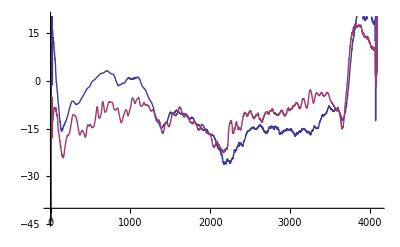

```mathematica
ListLinePlot[{testdata[[5;;4101]][[All,2]],testdata[[5;;4101]][[All,4]]},AxesOrigin->{0,-40}]
```

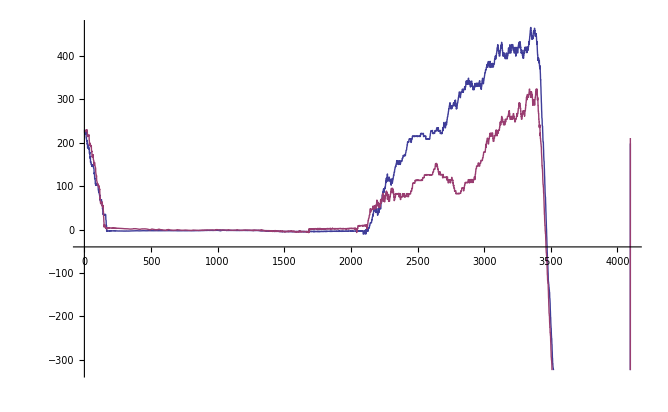

```mathematica
ListLinePlot[{testdata[[5;;4101]][[All,3]],testdata[[5;;4101]][[All,5]]},AxesOrigin->{0,-40}]
```

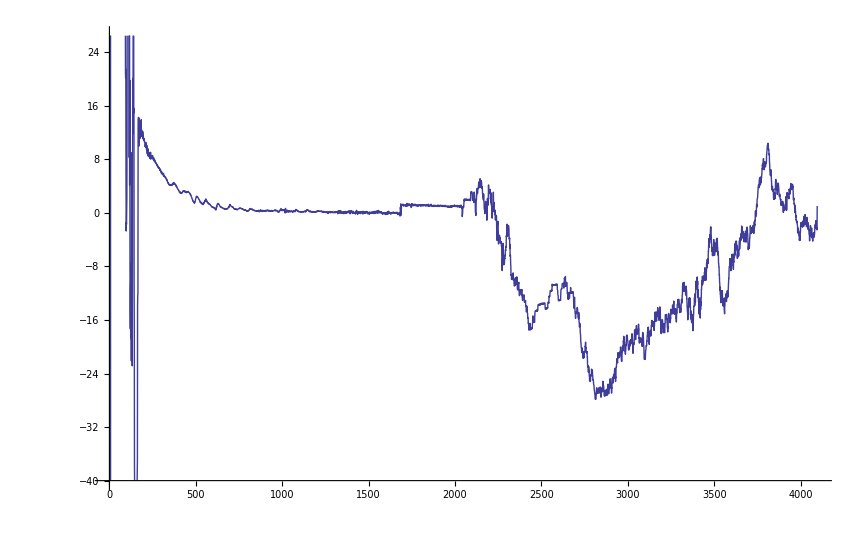

```mathematica
ListLinePlot[(testdata[[6;;4101]][[All,5]]-testdata[[6;;4101]][[All,3]])/testdata[[6;;4101]][[All,1]],AxesOrigin->{0,-40}]
```

```mathematica
ListLinePlot[{{1000*testdata[[5;;4101]][[All,1]],20*Log10[Abs[testdata[[5;;4101]][[All,4]]/testdata[[5;;4101]][[All,2]]]]}},AxesOrigin->{0,-30},PlotRange->All]
```

```mathematica
ListLinePlot[{{1000*testdata[[5;;4101]][[All,1]],20*Log10[Abs[testdata[[5;;4101]][[All,4]]]]},{1000*testdata[[5;;4101]][[All,1]],20*Log10[Abs[testdata[[5;;4101]][[All,2]]]]}},AxesOrigin->{0,-30},PlotRange->All]
```

```mathematica
listamp1=Table[{1000*testdata[[5;;4101]][[l,1]],20*Log10[testdata[[5;;4101]][[l,4]]]},{l,4097}];
listamp2=Table[{1000*testdata[[5;;4101]][[l,1]],20*Log10[testdata[[5;;4101]][[l,2]]]},{l,4097}];
listph1=Table[{1000*testdata[[5;;4101]][[l,1]],testdata[[5;;4101]][[l,5]]},{l,1600}];
listph2=Table[{1000*testdata[[5;;4101]][[l,1]],testdata[[5;;4101]][[l,3]]},{l,1600}];
```

```mathematica
listampratio=Table[{1000*testdata[[5;;4101]][[l,1]],20*Log10[Abs[testdata[[5;;4101]][[l,4]]/testdata[[5;;4101]][[l,2]]]]},{l,2,1600}];
listiTD=Table[{1000*testdata[[5;;4101]][[l,1]],(testdata[[5;;4101]][[l,5]]-testdata[[5;;4101]][[l,3]])*1000/(360*testdata[[5;;4101]][[l,1]])},{l,50,1600}];
listphD=Table[{1000*testdata[[5;;4101]][[l,1]],Abs[(testdata[[5;;4101]][[l,5]]-testdata[[5;;4101]][[l,3]])]},{l,50,1600}];
```

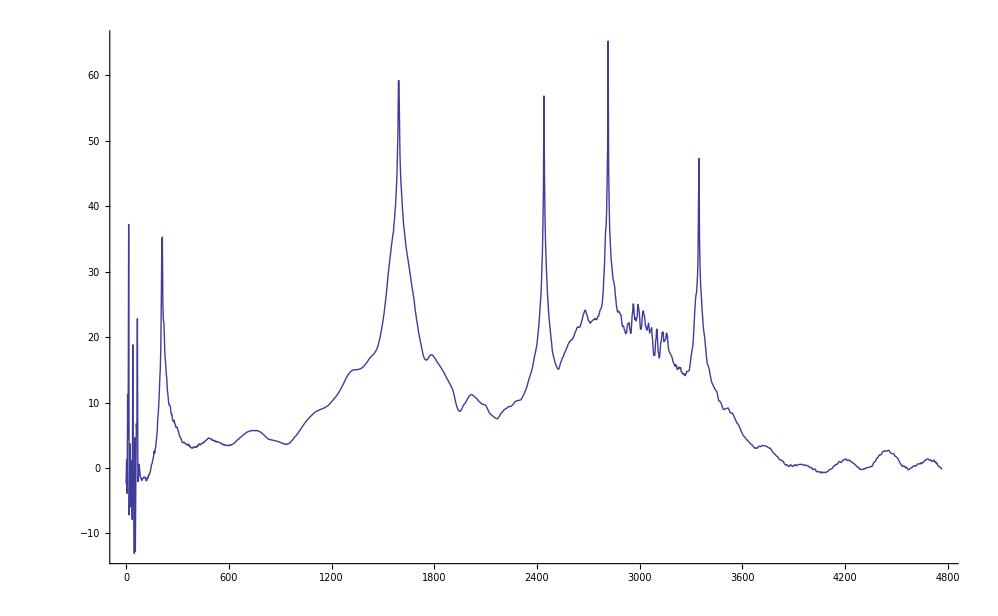

```mathematica
ListLinePlot[listampratio,AxesOrigin->{0,-30},PlotRange->All]
```

```mathematica
1000*testdata[[5;;4101]][[75,1]]
```

221.

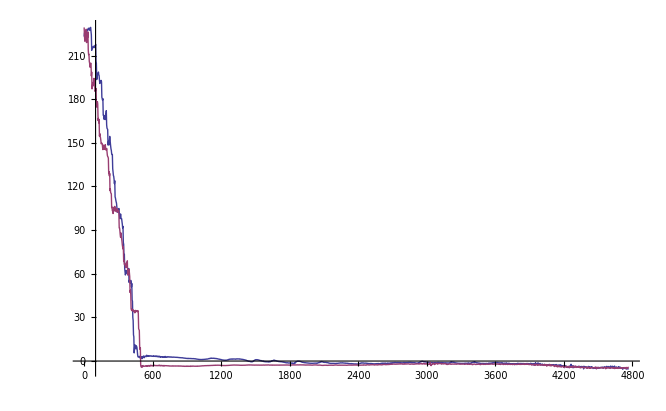

```mathematica
ListLinePlot[{listph1,listph2},PlotRange->All,AxesOrigin->{100,0}]
```

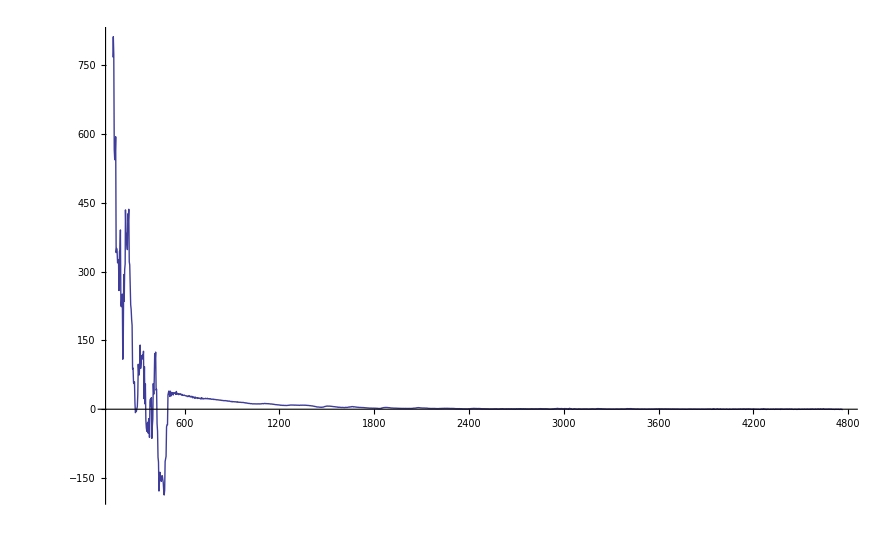

```mathematica
ListLinePlot[listiTD,PlotRange->All,AxesOrigin->{100,0}]
```